## percentages

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];
```

### 1+2 cases - automatic

```mathematica
Table[
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=If[case=="all",NotebookDirectory[]<>"percentage-data/all/result-gen"<>ToString[i]<>".h5",
NotebookDirectory[]<>"percentage-data/"<>case<>"/result"<>ToString[i]<>".h5"];
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];

,{i,If[case=="all",100,100]}];


type=Table[0,{i,Length[zeroFields]}];
Do[

If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";

ishow=i;
,{i,Length[zeroFields]}];

tallyList=SortBy[type//Tally,First];

EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]};
Print[tallyList,"\n", tallyList⟦All,2⟧];
Print[EandAll,1.0EandAll⟦1⟧/EandAll⟦2⟧];

,{case,{"all","posall-abfix","strong-constraints"}}]
```

{{A,70380},{B,70625},{C,683},{D,3135},{E,68}}
{70380,70625,683,3135,68}

{68,144891}0.000469318

{{A,231},{B,501},{C,754},{D,273},{E,329},{X:unknown,12}}
{231,501,754,273,329,12}

{329,2100}0.156667

{{A,85},{B,258},{C,3},{D,1},{E,2069},{X:unknown,49}}
{85,258,3,1,2069,49}

{2069,2465}0.839351

{Null,Null,Null}

X (also C, D when they are small) have been inspected by another program and it turns out that 
[231, 501, 754, 273, 329 + 12]
[85, 258 + 1, 0, 0, 2069 + 49 + 3]

## For α123β123 plots

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];

centralmodel=1.0{5.0,2.0,9.0,
1.0,0.0,1.2,0.0,
1.0,0.2,3.0,0.0,
0.5,0,0.7,
0,0,0};

xlist=1.0Subdivide[-4π,4π,39];
ylist=1.0Subdivide[-4π,4π,39];
labelPairs={{"a1","a2"},{"a2","a3"},{"a3","a1"},{"b1","b2"},{"b2","b3"},{"b3","b1"}};

mLs={};
Table[
mLs=Join[mLs,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0
,{x,xlist},{y,ylist}]//Flatten[#,1]&
];
,{label,labelPairs}];
Print[{"mLs size",mLs//Dimensions}];
```

{mLs size,{9600,17}}

```mathematica
(*do not run them again!!!*)
nkernal=100;
If[Mod[Length[mLs],nkernal]==0,Print["OK"],Interrupt[]];
mLss=Partition[mLs,Length[mLs]/nkernal];
Table[Export[NotebookDirectory[]<>"scan-a123b123-data/input"<>ToString[i]<>".h5",{"mLs"-> mLss⟦i⟧}],{i,Length[mLss]}];
```

OK

```mathematica
(*************)
(*************)

(**run python:*)
(*
command=Table[" python compute-a123b123.py "<>ToString[i]<>" & ",{i,1,nkernal}]//StringJoin
**)
(*copy the result as "plain text"*)
(*************)
(*running time, ~120min*)
```

```mathematica
(*import python result*)
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=NotebookDirectory[]<>"scan-a123b123-data/result"<>ToString[i]<>".h5";
If[FileExistsQ[datapath],
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];
mLnBFB=Join[mLnBFB,Import[datapath,"m_L_nBFB"]];
,
Print["not exist:"<>datapath];
];

,{i,nkernal(*{""}*)}];

Print[Length[Vmins]]
Dynamic[ishow]
```

1620

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];

type=Table[0,{i,Length[zeroFields]}];
Do[
ishow=i;
If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[zeroFields]}];

tallyList=type//Tally

Print[SortBy[%,First],
Length[seeds]
]
EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]}
1.0EandAll⟦1⟧/EandAll⟦2⟧
```

{{E,556},{A,709},{X:unknown,1},{C,91},{D,263}}

{{A,709},{C,91},{D,263},{E,556},{X:unknown,1}}1620

{556,1620}

0.34321

```mathematica
(**********************)
(*preparing for plots *)
(**********************)

δx=xlist⟦2⟧-xlist⟦1⟧;
δy=ylist⟦2⟧-ylist⟦1⟧;
plotgrid[xlist0_,ylist0_]:=Module[{xlist,ylist},

xlist=Append[xlist0-δx/2,xlist0⟦-1⟧+δx/2];

ylist=Append[ylist0-δy/2,ylist0⟦-1⟧+δy/2];
gridx=Table[Line[{{x,Min[ylist]},{x,Max[ylist]}}],{x,xlist}];
gridy=Table[Line[{{Min[xlist],y},{Max[xlist],y}}],{y,ylist}];
Graphics[{Gray,gridx,gridy}]
]
plotsamples[points_,color_]:=Graphics[{color,Table[Rectangle[point-{δx/2,δy/2},point+{δx/2,δy/2}],{point,points}]}]
```

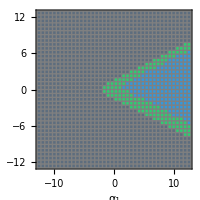
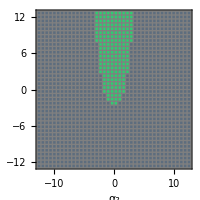
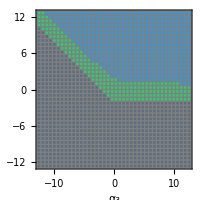
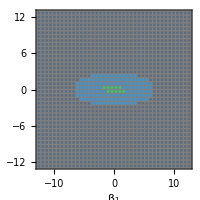
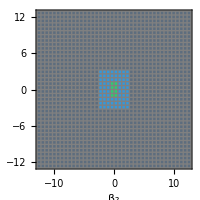
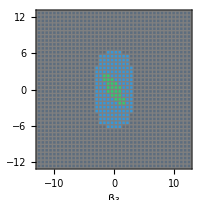

```mathematica
type2=type;
Do[type2⟦i⟧="E",{i,{130}}];
Do[type2⟦i⟧="E",{i,{426,447,422,420}}];

labelαβ={"a1"->"α_1","a2"->"α_2","a3"->"α_3","b1"->"β_1","b2"->"β_2","b3"->"β_3"};
plots=Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionE=Position[type2,"E"]//Flatten;
positionE=Select[positionE,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
plotE=plotsamples[pointE,RGBColor["#2ECC71"]];
positionA=Position[type2,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
positionA=Select[positionA,(Abs[mLs⟦#,otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionA}];
plotA=plotsamples[pointA,RGBColor["#3498DB"]];

mLnBFB0=Select[mLnBFB,(Abs[#⟦otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];

pointnBFB=Table[{mLnBFB0⟦pos,xid[xlabel]⟧,mLnBFB0⟦pos,xid[ylabel]⟧},{pos,Length[mLnBFB0]}];
plotnBFB=plotsamples[pointnBFB,RGBColor["#5D6D7E"]];

plot=Show[{plotE,plotA,plotnBFB,plotgrid[xlist,ylist]},PlotRange->{4π{-1,1},4π{-1,1}},
(*PlotRangeClipping->True,*)
PlotRangePadding->1.2{1,1},
Frame->True,Axes->False,ImageSize->200,FrameLabel->({xlabel,ylabel}/.labelαβ),AspectRatio->1];
(*Export["D:\\Dropbox\\mywork\\LR-scalar\\LR-V\\fig\\"<>xlabel<>ylabel<>".pdf",plot];*)
plot
,{label,labelPairs}
]
```

### Strange Samples Analysis

see data - analysis - v7.nb

## For m11m22 plots

Run all the code below, unless it has the comment "do not run them again!!!"

```mathematica
xstr={"m1q","m2q","m3q",
"L1","L2","L3","L4",
"r1","r2","r3","r4",
"a1","a2","a3",
"b1","b2","b3"};
xid=Association[Table[xstr⟦i⟧->i,{i,xstr//Length}]];

(*centralmodel=1.0{0.5,0.2,9.0,
1.0,0.0,1.2,0.0,
0.2,0.2,0.2,0.2,
0.3,0.3,0.3,
0,0,0};*)

centralmodel=1.0{0.5,0.2,9.0,
1.0,0.0,1.2,0.0,
0.0,r2bench=0.1,0.0,0.0,
0.3,0.3,0.3,
0,0,0};

xlist=1.0Subdivide[-4π,4π,39];
ylist=1.0Subdivide[-4π,4π,39];
labelPairs={{"r1","r3"}(*,{"r2","r3"}*)};

mLs={};
Table[
mLs=Join[mLs,
Table[model0=centralmodel;
model0⟦xid⟦label⟦1⟧⟧⟧=x;
model0⟦xid⟦label⟦2⟧⟧⟧=y;
model0
,{x,xlist},{y,ylist}]//Flatten[#,1]&
];
,{label,labelPairs}];
Print[{"mLs size",mLs//Dimensions}];
```

{mLs size,{1600,17}}

```mathematica
nkernal=10;
```

```mathematica
(*do not run them again!!!*)
(*CreateDirectory[NotebookDirectory[]<>"scan-mass-data/"<>"r2_"<>ToString[r2bench]];*)

If[Mod[Length[mLs],nkernal]==0,Print["OK"],Interrupt[]];
mLss=Partition[mLs,Length[mLs]/nkernal];

Table[Export[NotebookDirectory[]<>"scan-mass-data/input"<>ToString[i]<>".h5",{"mLs"-> mLss⟦i⟧}],{i,Length[mLss]}];
```

OK

```mathematica
(*do not run them again!!!*)
(*************)
(*************)

(**run python:*)

command=Table[" py compute-mass.py "<>ToString[i]<>" & ",{i,1,nkernal}]//StringJoin

(*copy the result as "plain text"*)
(*************)
(*running time, ~20min*)
```

py compute-mass.py 1 &  py compute-mass.py 2 &  py compute-mass.py 3 &  py compute-mass.py 4 &  py compute-mass.py 5 &  py compute-mass.py 6 &  py compute-mass.py 7 &  py compute-mass.py 8 &  py compute-mass.py 9 &  py compute-mass.py 10 &

```mathematica
(*import python result*)
zeroFields={};
mLs={};
xmins={};
Vmins={};
seeds={};
mLnBFB={};

Table[
datapath=NotebookDirectory[]<>"scan-mass-data/"<>"r2_"<>ToString[r2bench]<>"/result"<>ToString[i]<>".h5";
If[FileExistsQ[datapath],
zeroFields=Join[zeroFields,Import[datapath,"zerofields"]];
mLs=Join[mLs,Import[datapath,"m_L"]];
xmins=Join[xmins,Import[datapath,"x_min"]];
Vmins=Join[Vmins,Import[datapath,"V_min"]];
seeds=Join[seeds,Import[datapath,"seed"]];
mLnBFB=Join[mLnBFB,Import[datapath,"m_L_nBFB"]];
,
Print["not exist:"<>datapath];
];

,{i,nkernal(*{""}*)}];

Print[Length[Vmins]]
Dynamic[ishow]
```

700

```mathematica
If[mLs⟦1,xid["r2"]⟧≠ r2bench,Interrupt[],Print["r2 bench checked! r2bench should be ",r2bench]]
```

r2 bench checked! r2bench should be 0.1

```mathematica
same[x1_,x2_,ϵ_:10^-4]:=Abs[(Abs[x1]-Abs[x2])]<ϵ

badDueToA[xmin_]:=same[Table[xmin⟦j⟧,{j,1,2}]//Abs//Max,0];
badDueToB[xmin_]:=same[Table[xmin⟦j⟧,{j,3,8}]//Abs//Max,0];
badDueToC[xmin_]:=Not[same[det2[xmin]//Abs//Max,0]];
(*badDueToD[xmin_]:=And[same[xmin⟦3⟧,xmin⟦6⟧],same[xmin⟦4⟧,xmin⟦7⟧],same[xmin⟦5⟧,xmin⟦8⟧]];*)
badDueToD[xmin_]:=same[xmin⟦3⟧^2+2 xmin⟦4⟧^2+xmin⟦5⟧^2,xmin⟦6⟧^2+2 xmin⟦7⟧^2+xmin⟦8⟧^2];
goodE[xmin_]:=Or[same[xmin⟦1⟧,xmin⟦2⟧,10^-2],same[xmin⟦3⟧xmin⟦5⟧,0]&&same[xmin⟦4⟧,0]&&same[xmin⟦6⟧xmin⟦8⟧,0]&&same[xmin⟦7⟧,0]];

type=Table[0,{i,Length[zeroFields]}];
Do[
ishow=i;
If[badDueToA[xmins⟦i⟧],
type⟦i⟧="A";Continue[]
];
If[badDueToB[xmins⟦i⟧],
type⟦i⟧="B";Continue[]
];
If[badDueToC[xmins⟦i⟧],
type⟦i⟧="C";Continue[]
];
If[badDueToD[xmins⟦i⟧],
type⟦i⟧="D";Continue[]
];

If[goodE[xmins⟦i⟧],
type⟦i⟧="E";Continue[]
];

type⟦i⟧="X:unknown";


,{i,Length[zeroFields]}];

tallyList=type//Tally

Print[SortBy[%,First],
Length[seeds]
]
(*EandAll={Select[tallyList,#⟦1⟧=="E"&]⟦1,2⟧,Length[seeds]}
1.0EandAll⟦1⟧/EandAll⟦2⟧*)
```

{{D,577},{E,100},{C,23}}

{{C,23},{D,577},{E,100}}700

```mathematica
(**********************)
(*preparing for plots *)
(**********************)

δx=xlist⟦2⟧-xlist⟦1⟧;
δy=ylist⟦2⟧-ylist⟦1⟧;
plotgrid[xlist0_,ylist0_]:=Module[{xlist,ylist},

xlist=Append[xlist0-δx/2,xlist0⟦-1⟧+δx/2];

ylist=Append[ylist0-δy/2,ylist0⟦-1⟧+δy/2];
gridx=Table[Line[{{x,Min[ylist]},{x,Max[ylist]}}],{x,xlist}];
gridy=Table[Line[{{Min[xlist],y},{Max[xlist],y}}],{y,ylist}];
Graphics[{Gray,gridx,gridy}]
]
plotsamples[points_,color_]:=Graphics[{color,Table[Rectangle[point-{δx/2,δy/2},point+{δx/2,δy/2}],{point,points}]}]
```

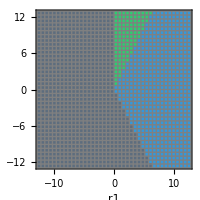

```mathematica
type2=type;
(*Do[type2⟦i⟧="E",{i,{130}}];
Do[type2⟦i⟧="E",{i,{426,447,422,420}}];
*)

labelαβ={"a1"->"α_1","a2"->"α_2","a3"->"α_3","b1"->"β_1","b2"->"β_2","b3"->"β_3"};
plots=Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
otherId=Delete[Range[Length[xstr]],{{xid[xlabel]},{xid[ylabel]}}];
positionE=Position[type2,"E"]//Flatten;
pointE=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionE}];
plotE=plotsamples[pointE,RGBColor["#2ECC71"]];
positionA=Position[type2,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
pointA=Table[{mLs⟦pos,xid[xlabel]⟧,mLs⟦pos,xid[ylabel]⟧},{pos,positionA}];
plotA=plotsamples[pointA,RGBColor["#3498DB"]];

mLnBFB0=Select[mLnBFB,(Abs[#⟦otherId⟧-centralmodel⟦otherId⟧]//Max)<10^-6&];

pointnBFB=Table[{mLnBFB0⟦pos,xid[xlabel]⟧,mLnBFB0⟦pos,xid[ylabel]⟧},{pos,Length[mLnBFB0]}];
plotnBFB=plotsamples[pointnBFB,RGBColor["#5D6D7E"]];

plot=Show[{plotE,plotA,plotnBFB,plotgrid[xlist,ylist]},PlotRange->{4π{-1,1},4π{-1,1}},
(*PlotRangeClipping->True,*)
PlotRangePadding->1.2{1,1},
Frame->True,Axes->False,ImageSize->200,FrameLabel->({xlabel,ylabel}/.labelαβ),AspectRatio->1];
(*Export["D:\\Dropbox\\mywork\\LR-scalar\\LR-V\\fig\\"<>xlabel<>ylabel<>".pdf",plot];*)
plot
,{label,labelPairs}
]
```

```mathematica
{RGBColor["#2ECC71"],RGBColor["#3498DB"],RGBColor["#5D6D7E"]}
```

{RGBColor[0.1803921568627451, 0.8, 0.44313725490196076],RGBColor[0.20392156862745098, 0.596078431372549, 0.8588235294117647],RGBColor[0.36470588235294116, 0.42745098039215684, 0.49411764705882355]}

### check if blue region contains local type E? (answer: not found anyone in this case)

```mathematica
(*positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
Table[Table[minimize[mLs⟦pos⟧,rndseed],{rndseed,10}],
{pos,positionA⟦1;;1⟧}]*)
```

```mathematica
sol′extract[sol_]:={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}/.sol;
```

```mathematica
Is′typeE[xmin_]:=And[Not[badDueToA[xmin]],
Not[badDueToB[xmin]],
Not[badDueToC[xmin]],
Not[badDueToD[xmin]],
goodE[xmin]];
```

```mathematica
(*Table[Is′typeE[xmins⟦pos⟧],{pos,positionE}]*)
```

```mathematica
positionA//Length
```

600

```mathematica
positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;
check′result=Table[
local′type′E=False;
xmin′use=xmins⟦pos⟧;
Do[minsol=minimize[mLs⟦pos⟧,rndseed];
(*Print[minsol];*)
minsolc=sol′extract[minsol⟦2⟧];
If[Is′typeE[minsolc],local′type′E=True;xmin′use=minsolc;Break[]]
,{rndseed,10}];
{local′type′E,xmin′use},
{pos,positionA⟦101;;600⟧}];//Timing
```

{1314.71,Null}

```mathematica
Position[check′result,True]
```

{}

### corresponding mass distributions

```mathematica
massfromλ[λ_(*potential para*),xmin_(*xmin*)]:=(*normalized v scale to 246GeV*)Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,(**)
vevRep,
other
},
{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=λ;
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=canonicalize[xmin];


vevRep={(*Print[{f1,g1}];*)θL->f1-g1(*Warning: what if g1 are nonzero*),α->t2,vL->x1,vR->y1,myk1->k1,myk2->k2};

{"M11"->(r3-2 r1)vR^2+a3/2 (k1^2-k2^2),
"M22"->(4r2)vR^2+a3/2 (k1^2-k2^2),
"246GeV"->√(k1^2+k2^2)(*246.0/(√2)=173.xxx*)}/.vevRep]
```

```mathematica
maxabs[x_]:=Max[Abs[x]];

iσ2Transform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k2,k1,-x3,-x2,-x1,-y3,-y2,-y1,t2+0,f3,f2,f1,g3,g2,g1}
]

parityTransform[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;
{k1,k2,y1,y2,y3,x1,x2,x3,-t2,g1,g2,g3,f1,f2,f3}
]



canonicalize[xmin_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3,(**)
exchange123,temp},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=xmin;
If[maxabs[{x1,x2,x3}]>maxabs[{y1,y2,y3}],
(*exchange123={x1,x2,x3};{x1,x2,x3}={y1,y2,y3};{y1,y2,y3}=exchange123;
t2=-t2;*)
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=parityTransform[xmin]
];
(*If[Abs[x1]<Abs[x3],temp=x1;x1=x3;x3=temp];
If[Abs[y1]<Abs[y3],temp=y1;y1=y3;y3=temp];*)
If[Abs[y1]<Abs[y3],{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=iσ2Transform[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}]
];


If[x1<0,x1=-x1;f1=f1+π];
If[y1<0,y1=-y1;g1=g1+π];
If[k1<0,k1=-k1;t2=t2+π];
If[k2<0,k2=-k2;t2=t2+π];
(*If[same[Vatx[mλ,xmin],
Vatx[mλ,xmin//canonicalize]],Interrupt[]]*)
If[Or[k1<0,k2<0,x1<0,y1<0,Abs[x2]>0.1,Abs[x3]>0.1,Abs[y2]>0.1,Abs[y3]>0.1],
Print["bad vacuum, unable to canonicalize, ",posOutput,{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}](*Interrupt[]*)];
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}
]
```

```mathematica
chargedMasses[rule_]:=(*x^2*)((*x->*)(246(*GeV*))/("246GeV"))^2{"M11","M22"}/.rule
```

```mathematica
(*plotsamples[pointE,RGBColor["#2ECC71"]]*)
```

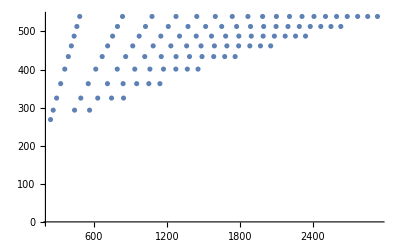

```mathematica
Table[
xlabel=label⟦1⟧;
ylabel=label⟦2⟧;
positionEall=Position[type,"E"]//Flatten;
positionE=positionEall;

positionA=Position[type,_?(MemberQ[{"A","B","C","D"},#]&)]//Flatten;

plot′raw=(pointsGM=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionE}])//ListPlot[#,PlotRange->All]&
(*plotA=Table[posOutput=pos;massfromλ[mLs⟦pos⟧,xmins⟦pos⟧//canonicalize]//chargedMasses//Sqrt,{pos,positionA}]//ListPlot[#,PlotRange->All]&*)
,{label,labelPairs⟦1;;1⟧}
]
```

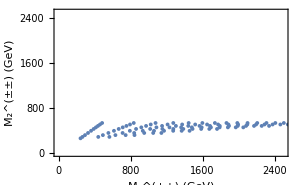

```mathematica
plot=Show[plot′raw,PlotRange->{{0,2500},{0,2500}},Frame->True,Axes->False,FrameLabel->{"M_1^(±±) (GeV)","M_2^(±±) (GeV)"},ImageSize->300]
```

```mathematica
Export[NotebookDirectory[]<>"scan-mass-data/masspoints_r2_"<>ToString[r2bench]<>".h5",{"m1m2inGeV"->pointsGM}]
```

D:\Dropbox\mywork\LR-scalar\code-2\scan-mass-data/masspoints_r2_0.1.h5

## Function

```mathematica
det2[x_]:=Module[{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},
{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;Abs[{-ⅇ^(2 ⅈ f2) x2^2-ⅇ^(ⅈ f1+ⅈ f3) x1 x3,-ⅇ^(2 ⅈ g2) y2^2-ⅇ^(ⅈ g1+ⅈ g3) y1 y3}]
]

minimize[c_,min′rndseed_:0,fix_:{}]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

variables={k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3};
If[Length[fix]>0,Do[variables=DeleteCases[variables,var];,{var,fix⟦All,1⟧}] ];

NMinimize[1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]/.fix
,variables,Method->{Automatic,RandomSeed->min′rndseed}]//Quiet
]
Vatx[c_,x_]:=Module[{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3,
(**)
k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3},{m1q,m2q,m3q,L1,L2,L3,L4,r1,r2,r3,r4,a1,a2,a3,b1,b2,b3}=c;

{k1,k2,x1,x2,x3,y1,y2,y3,t2,f1,f2,f3,g1,g2,g3}=x;

1/4 (k1^4 L1+k2^4 L1+2 k2^2 (-m1q+a3 (x1^2+x2^2+y1^2+y2^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+2 k1^2 (k2^2 (L1+2 L3)-m1q+a3 (x2^2+x3^2+y2^2+y3^2)+a1 (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2))+4 (4 r2 x2^4+4 r2 x1^2 x3^2+r3 x1^2 y1^2+2 r3 x2^2 y1^2+r3 x3^2 y1^2+2 r3 x1^2 y2^2+4 r3 x2^2 y2^2+2 r3 x3^2 y2^2+4 r2 y2^4+(r3 (x1^2+2 x2^2+x3^2)+4 r2 y1^2) y3^2-m3q (x1^2+2 x2^2+x3^2+y1^2+2 y2^2+y3^2)+r1 ((x1^2+2 x2^2+x3^2)^2+(y1^2+2 y2^2+y3^2)^2)))+8 r2 x1 x2^2 x3 Cos[f1-2 f2+f3]+b2 k1^2 x1 y1 Cos[f1-g1]+8 r4 x2^2 y2^2 Cos[2 f2-2 g2]+8 r4 x1 x3 y2^2 Cos[f1+f3-2 g2]+b1 k1^2 x2 y2 Cos[f2-g2]+b1 k2^2 x2 y2 Cos[f2-g2]+b3 k1^2 x3 y3 Cos[f3-g3]+8 r4 x2^2 y1 y3 Cos[2 f2-g1-g3]+8 r4 x1 x3 y1 y3 Cos[f1+f3-g1-g3]+8 r2 y1 y2^2 y3 Cos[g1-2 g2+g3]+b3 k2^2 x1 y1 Cos[f1-g1-2 t2]+b1 k1 k2 x1 y1 Cos[f1-g1-t2]+2 b3 k1 k2 x2 y2 Cos[f2-g2-t2]+k1^3 k2 L4 Cos[t2]+k1 k2^3 L4 Cos[t2]-2 k1 k2 m2q Cos[t2]+2 a2 k1 k2 x1^2 Cos[t2]+4 a2 k1 k2 x2^2 Cos[t2]+2 a2 k1 k2 x3^2 Cos[t2]+2 a2 k1 k2 y1^2 Cos[t2]+4 a2 k1 k2 y2^2 Cos[t2]+2 a2 k1 k2 y3^2 Cos[t2]+2 k1^2 k2^2 L2 Cos[2 t2]+2 b2 k1 k2 x2 y2 Cos[f2-g2+t2]+b1 k1 k2 x3 y3 Cos[f3-g3+t2]+b2 k2^2 x3 y3 Cos[f3-g3+2 t2]

]
```